This computes quantiles of the inner slope of the exponential profile from Hooper+Witte 2017 (arXiv:1610.07587).

```mathematica
pdf[γ_,γbar_:0.74,σ_:0.42,κ_:0.10]:=1/(√(2π))1/(σ-κ(γ-γbar))Exp[-Log[1-(κ(γ-γbar))/σ]^2/(2 κ^2)]
```

```mathematica
γbar=0.74;
σ=0.42;
κ=0.10;
```

```mathematica
Integrate[pdf[γ],{γ,0,0.54}]
```

0.268579

```mathematica
expDistro[γbar_:0.74,σ_:0.42,κ_:0.10]=ProbabilityDistribution[
1/(√(2π))1/(σ-κ(γ-γbar))Exp[-Log[1-(κ(γ-γbar))/σ]^2/(2 κ^2)],
{γ,0,σ/κ+γbar}
]
```

```mathematica
σ/κ+γbar
```

4.94

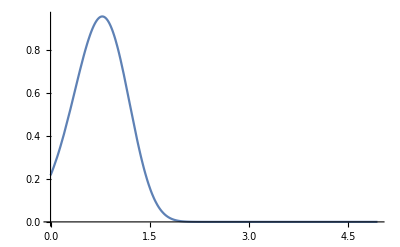

```mathematica
Plot[PDF[expDistro[],γ],{γ,0,4.94}]
```

```mathematica
Table[Quantile[expDistro[],i],{i,0.1,0.9,0.1}]
```

{0.28594,0.450207,0.577731,0.689375,0.794874,0.901285,1.01681,1.15728,1.38515}